```mathematica
parse[s_]:=ToExpression@StringReplace[s,{" "->"", "("->"{",")"->"}","Vector("->"{","E"->"*10^"}]
```

```mathematica
model=a x^n+c;
```

```mathematica
(*model=a n^x+c;*)
```

```mathematica
fitDegree[data_]:=FindFit[data,model,{a,n,c},x]
```

```mathematica
plotTogehter[data_, rule_]:=With[{expr=model/.rule},
Show[
Plot[expr,{x,data[[1,1]],data[[-1,1]]}],
ListPlot[data,PlotStyle->Red],PlotLabel->expr]]
```

```mathematica
fitAndPlot[data_]:=plotTogehter[data,fitDegree[data]]
```

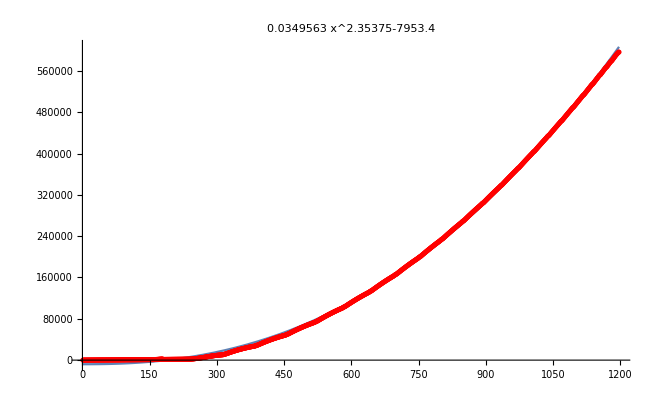

```mathematica
s=ReadString[NotebookDirectory[]<> "FitterData.txt"];
fitAndPlot[Take[parse[s]]]
```